### Visualize Network

#### Visualize Network Pattern

```mathematica
VisualizeNetwork[
network:
{neurons:{{symbol_Symbol,index_Integer,previousState_Integer,currentState_Integer}..}, 
synapses:{{_Integer..}..}}];
```

```mathematica
VisualizeNetwork[neurons_,synapseStateDiagram_]:=
Block[{vertices,synapsePosition,edges,synapseStates},
vertices=Range[Length[neurons]];
synapsePosition = Position[synapseStateDiagram,1|2];
edges=Apply[Rule,synapsePosition,{1}];
synapseStates=Extract[synapseStateDiagram,synapsePosition];
Graph[
vertices,
edges,VertexSize->0.1,
VertexShapeFunction->Thread[vertices->visualizeNeuron/@neurons],
EdgeShapeFunction->Thread[edges->visualizeSynapse/@synapseStates]]]
```

#### Visualize Neuron Function

State Mappings

0 = Light Gray = Inactive 
1 = Green = Active 
2 = Orange = Predictive

func specifies that each vertex should be rendered with the primitives provided by func[{x,y},v,{w,h}], where {x,y} is the center, v the vertex name, and {w,h} the width and the height.

```mathematica
visualizeNeuron[{previousState_,currentState_}]:=
With[{colorList={LightGray,Green,Orange}},
Function[{position,name,dimensions},
{EdgeForm[Black],colorList[[previousState+1]],Disk[position,Min[dimensions],{0,Pi}],
EdgeForm[Black],colorList[[currentState+1]],Disk[position,Min[dimensions],{Pi,2Pi}]}]]
```

#### Visualize Synapse Function

State Mappings

1 = Potential
2 = Permanent

func[{{x_1,y_1},{x_2,y_2},…},v<->w], where {{x_1,y_1},{x_2,y_2},…} are line segments and v<->w is the edge.

```mathematica
visualizeSynapse[state_]:=
Function[{pts,e},
Which[
state==1,
{Dashed,{Arrowheads[Large],Arrow[pts]}},
state==2,
{Thick,{Arrowheads[Large],Arrow[pts]}}]]
```

```mathematica
({{0, 2}, {2, 0}, {0, 2}})
```

```mathematica
Position[({{0, 1, 0}, {0, 0, 2}, {2, 0, 0}}),1|2]
```

{{1,2},{2,3},{3,1}}

```mathematica
({{0, 1, 0}, {0, 0, 2}, {2, 0, 0}})
```

{{0,1,0},{0,0,2},{2,0,0}}

```mathematica
m={{0,1,0},{0,0,2},{2,0,0}}
```

{{0,1,0},{0,0,2},{2,0,0}}

```mathematica
Extract[m,{{1,2},{2,3},{3,1}}]
```

{1,2,2}

{1→2,2→3,3→1}

```mathematica
{{0,2},{2,0},{0,2}}//MatrixForm
```

```mathematica
VisualizeNetwork[{{}},{{}}]
```

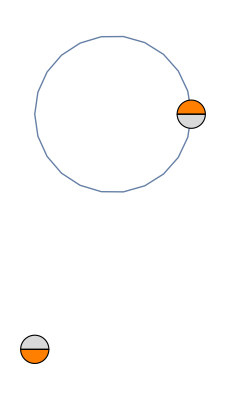

```mathematica
VisualizeNetwork[({{0, 2}, {2, 0}}),({{0, 0}, {0, 2}})]
```

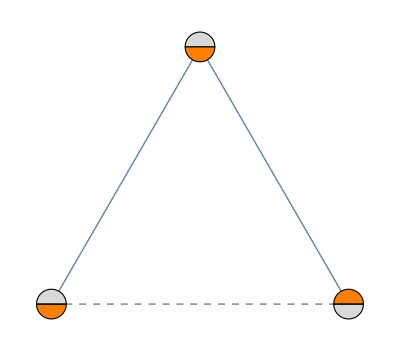

```mathematica
VisualizeNetwork[({{0, 2}, {2, 0}, {0, 2}}),({{0, 1, 0}, {0, 0, 2}, {2, 0, 0}})]
```

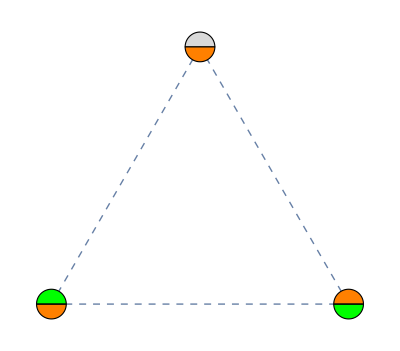

```mathematica
VisualizeNetwork[({{1, 2}, {2, 1}, {0, 2}}),({{0, 1, 0}, {0, 0, 1}, {1, 0, 0}})]
```

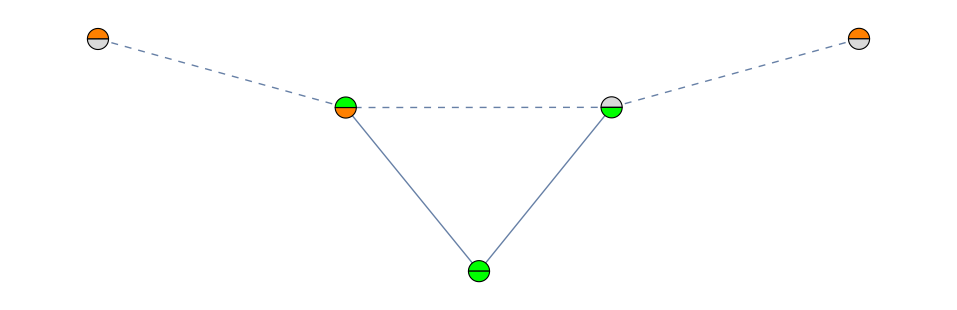

```mathematica
VisualizeNetwork[({{0, 1}, {1, 2}, {1, 1}, {2, 0}, {2, 0}}),({{0, 1, 0, 0, 0}, {0, 0, 2, 0, 0}, {2, 0, 0, 0, 0}, {1, 0, 0, 0, 0}, {0, 1, 0, 0, 0}})]
```

```mathematica
VisualizeNetwork[neurons_,synapseStateDiagram_]
```